# Procedural Programming Part 2

## Basic Exercises

### Question Subsection

In what follows, x is a list of values from 0 to 10 in increments of 0.1. y is a list of zeros with the same length as x. You can think of y as a placeholder list. Use a For loop to update the placeholder y with the values of Sin[x]. Plot it using ListPlot.

```mathematica
x=Range[0,10,0.1];
y=Table[0,Length[x]];
```

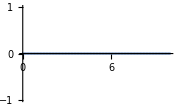

```mathematica
ListPlot[Thread[{x,y}],ImageSize->Small]
```

#### Solution

```mathematica
For[i=1,i≤Length[x],i++,y[[i]]=Sin[x[[i]]]]
```

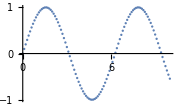

```mathematica
ListPlot[Thread[{x,y}],ImageSize->Small]
```

### Question Subsection

Let’s write a little game. You can use Input[] to prompt the user to input a value. Let’s have the computer pick a random integer between 0 and 10, and prompt the user to guess it until the user finds the right value.

```mathematica
?Input
```

Input[] interactively reads in one Wolfram Language expression. 
Input[prompt] requests input, displaying prompt as a "prompt".
Input[prompt,init] in a notebook front end uses init as the initial contents of the input field.

#### Hint

If you accidentally get into an infinite loop, you can quit the kernel from the Evaluation tab in the menu bar.

#### Solution

```mathematica
x=RandomInteger[{0,10}];
guess=Input["Enter your initial guess"];
While[guess≠x,guess=Input["Nope, guess again."]]
Print["Yay!!! The answer is ",guess,"!!! :) :) :)"]
```

Yay!!! The answer is 4!!! :) :) :)

### Question Subsection

Given 100 random integers between 0 and 100, loop over them with a Do loop and print out the ones that are simultaneously divisible by 3 and 5.

```mathematica
numbers=Table[RandomInteger[{0,100}],100];
```

#### Solution

```mathematica
Do[If[Mod[n,5]==0 && Mod[n,3]==0,Print[n]],{n,numbers}]
```

60

0

75

45

45

45

30

30

0

Or Alternatively:

```mathematica
Do[If[Mod[n,15]==0==0,Print[n]],{n,numbers}]
```

60

0

75

45

45

45

30

30

0

## Advanced Exercises

### Question Subsection

Recall the Newton-Raphson method we showed in Lesson 15: Functional Programming Part 2. Implement it using the While loop instead of FixedPoint.

#### Solution

```mathematica
Newton[xn_,f_,fp_]:=xn-f[xn]/fp[xn];
new=Input["Initial guess"];
prev=new;
new=Newton[prev,Function[x,x^2-1],Function[x,2x]];
While[Abs[new-prev]>0.0001,
prev=new;
new=Newton[prev,Function[x,x^2-1],Function[x,2x]];
]
ans=new
```